```mathematica
Exit
```

```mathematica
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]

Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]

Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Experiments","ActionAngleConfidenceSampler.m"}]
]
```

```mathematica
n=40;
(*r=ConstantArray[2./n,n];*)
confidence=0.95;
radius=0.001;
chunksize=1000000;
maxsamplecount=100000000;

verboseQ=False;

"True squared gyradius"->1./3(n+1)/n^2(n/2)^2
```

True squared gyradius→3.41667

```mathematica
resultAAM=ActionAngleConfidenceSample[n,radius,
"MaxSamples"->maxsamplecount,
"ConfidenceLevel"->confidence,
"ChunkSize"->chunksize,
"Progressive"->verboseQ
];
Dataset[resultAAM]
```

Compiling cActionAngleConfidenceSample_...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 1.20737 s.

```mathematica
resultPAAM=ActionAngleConfidenceSample[n,radius,
"MaxSamples"->maxsamplecount,
"ConfidenceLevel"->confidence,
"ChunkSize"->chunksize,
"Progressive"->True,
"Verbose"->verboseQ
];
Dataset[resultPAAM]
```

```mathematica
resultCoBarS=CycleConfidenceSample["SquaredGyradius",3,ConstantArray[1.,n],radius,
"SphereRadii"->"SymplecticQuotient",
"QuotientSpace"->True,
"ConfidenceLevel"->confidence,
"MaxSamples"->maxsamplecount,
"ChunkSize"->chunksize,
"Verbose"->verboseQ
];
Dataset[resultCoBarS]
```

Compiling cConfidenceSampleRandomVariables[3]...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 2.39624 s.

```mathematica
relativeRadius=.
```

```mathematica
confidence=0.95;
chunksize=10000;
maxsamplecount=100000000;

Dynamic[relativeRadius]
Dynamic[n]


resultCoBarS=Association[
Table[
relativeRadius->Table[
KeyDrop[{"r","ρ"}]@CycleConfidenceSample["SquaredGyradius",3,ConstantArray[1.,n],relativeRadius,
"SphereRadii"->"SymplecticQuotient",
"QuotientSpace"->True,
"ConfidenceLevel"->confidence,
"MaxSamples"->maxsamplecount,
"ChunkSize"->chunksize,
"RelativeErrorMode"->True,
"Verbose"->False
],
{n,8,100,4}],

{relativeRadius,{0.1,0.01,0.001}}]
];
```

```mathematica
resultCoBarS
```

<|0.1→{{8,0.147881},{12,0.147032},{16,0.169112},{20,0.19102},{24,0.214296},{28,0.252819},{32,0.264542},{36,0.305286},{40,0.324113},{44,0.361249},{48,0.382398},{52,0.409149},{56,0.41626},{60,0.448035},{64,0.488406},{68,0.504299},{72,0.510256},{76,0.540987},{80,0.567865},{84,0.597681},{88,0.610015},{92,0.634421},{96,0.666722},{100,0.696088}},0.01→{{8,0.122426},{12,0.149353},{16,0.165516},{20,0.184801},{24,0.217436},{28,0.251503},{32,0.266714},{36,0.290569},{40,0.328704},{44,0.332591},{48,0.383556},{52,0.403556},{56,0.413277},{60,0.443225},{64,0.496605},{68,0.508119},{72,0.519003},{76,0.552872},{80,0.571096},{84,0.590842},{88,0.632618},{92,0.640021},{96,0.664303},{100,0.70643}},0.001→{{8,0.12646},{12,0.149219},{16,0.161467},{20,0.193981},{24,0.216505},{28,0.239949},{32,0.274006},{36,0.309217},{40,0.32746},{44,0.35964},{48,0.380684},{52,0.397055},{56,0.413588},{60,0.466939},{64,0.460375},{68,0.511206},{72,0.51564},{76,0.5598},{80,0.555844},{84,0.58558},{88,0.608125},{92,0.641433},{96,0.660779},{100,0.681833}}|>

```mathematica
relativeRadius->Values/@resultCoBarS[[All,{"EdgeCount","Timing"}]]]
```

<|0.001→{{8,0.138247},{12,0.134182},{16,0.160788},{20,0.182715},{24,0.217792},{28,0.242708},{32,0.272565},{36,0.29603},{40,0.324226},{44,0.340553},{48,0.359233},{52,0.396805},{56,0.405419},{60,0.460317},{64,0.485595},{68,0.495784},{72,0.51209},{76,0.55684},{80,0.575909},{84,0.577254},{88,0.620927},{92,0.646273},{96,0.670373},{100,0.675783}}|>

<|0.1→{{8,0.147881},{12,0.147032},{16,0.169112},{20,0.19102},{24,0.214296},{28,0.252819},{32,0.264542},{36,0.305286},{40,0.324113},{44,0.361249},{48,0.382398},{52,0.409149},{56,0.41626},{60,0.448035},{64,0.488406},{68,0.504299},{72,0.510256},{76,0.540987},{80,0.567865},{84,0.597681},{88,0.610015},{92,0.634421},{96,0.666722},{100,0.696088}},0.01→{{8,0.122426},{12,0.149353},{16,0.165516},{20,0.184801},{24,0.217436},{28,0.251503},{32,0.266714},{36,0.290569},{40,0.328704},{44,0.332591},{48,0.383556},{52,0.403556},{56,0.413277},{60,0.443225},{64,0.496605},{68,0.508119},{72,0.519003},{76,0.552872},{80,0.571096},{84,0.590842},{88,0.632618},{92,0.640021},{96,0.664303},{100,0.70643}},0.001→{{8,0.12646},{12,0.149219},{16,0.161467},{20,0.193981},{24,0.216505},{28,0.239949},{32,0.274006},{36,0.309217},{40,0.32746},{44,0.35964},{48,0.380684},{52,0.397055},{56,0.413588},{60,0.466939},{64,0.460375},{68,0.511206},{72,0.51564},{76,0.5598},{80,0.555844},{84,0.58558},{88,0.608125},{92,0.641433},{96,0.660779},{100,0.681833}}|>

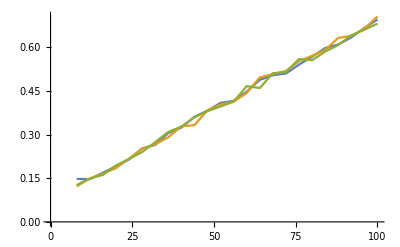

```mathematica
ListLinePlot[{resultCoBarS[[1]],resultCoBarS[[2]],resultCoBarS[[3]]}]
```

```mathematica
resultCoBarS
```

```mathematica
ExprectedMeans=AssociationThread[
Length/@resultCoBarS[[All,"r"]],
resultCoBarS[[All,"SampleMean"]]
];
```

```mathematica
Dynamic[n]
resultCoBarS=Table[
KeyDrop[{"r","ρ"}]@CycleConfidenceSample["SquaredGyradius",3,ConstantArray[1.,n],relativeRadius ExprectedMeans[n],
"SphereRadii"->"SymplecticQuotient",
"QuotientSpace"->True,
"ConfidenceLevel"->confidence,
"MaxSamples"->maxsamplecount,
"ChunkSize"->chunksize,
"RelativeErrorMode"->True,
"Verbose"->verboseQ
],
{n,8,100,4}];
```

{<|EdgeCount→8,Timing→0.138247|>,<|EdgeCount→12,Timing→0.134182|>,<|EdgeCount→16,Timing→0.160788|>,<|EdgeCount→20,Timing→0.182715|>,<|EdgeCount→24,Timing→0.217792|>,<|EdgeCount→28,Timing→0.242708|>,<|EdgeCount→32,Timing→0.272565|>,<|EdgeCount→36,Timing→0.29603|>,<|EdgeCount→40,Timing→0.324226|>,<|EdgeCount→44,Timing→0.340553|>,<|EdgeCount→48,Timing→0.359233|>,<|EdgeCount→52,Timing→0.396805|>,<|EdgeCount→56,Timing→0.405419|>,<|EdgeCount→60,Timing→0.460317|>,<|EdgeCount→64,Timing→0.485595|>,<|EdgeCount→68,Timing→0.495784|>,<|EdgeCount→72,Timing→0.51209|>,<|EdgeCount→76,Timing→0.55684|>,<|EdgeCount→80,Timing→0.575909|>,<|EdgeCount→84,Timing→0.577254|>,<|EdgeCount→88,Timing→0.620927|>,<|EdgeCount→92,Timing→0.646273|>,<|EdgeCount→96,Timing→0.670373|>,<|EdgeCount→100,Timing→0.675783|>}

```mathematica
Dataset/@resultCoBarS
```

{,,,,,,,,,,,,,,,,,,,,,,,,}

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100}

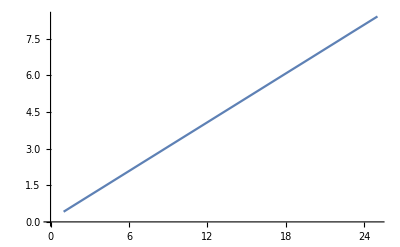

```mathematica
ListLinePlot[resultCoBarS[[All,"SampleMean"]]]
```